```mathematica
denom = Series[√(ψ^2+ 1/ϵ$s d^2/λ$D^2+ I d^2/λ$d^2),{λ$D,0,1}] // Normal // PowerExpand // Expand
```

d/(√ϵ$s λ$D)+(ⅈ d √ϵ$s λ$D)/(2 λ$d^2)+(√ϵ$s λ$D ψ^2)/(2 d)

```mathematica
d/(√ϵ$s λ$D)+(√ϵ$s λ$D ψ^2)/(2 d)
```

```mathematica
denom/((√ϵ$s λ$D)/(2 d)) // Simplify
```

d^2 (ⅈ/λ$d^2+2/(ϵ$s λ$D^2))+ψ^2

```mathematica
INtegrate
```

```mathematica
θ$red= 1/ϵ$s 1/(1 - (I k$D^2 λ$d^2)/ϵ$s)(1 - (I k$D^2 λ$d^2)/ϵ$s ψ/(√(ψ^2+ (k$D^2 d^2)/ϵ$s+ I d^2/λ$d^2)))  /. {k$D-> 1/λ$D}
```

```mathematica
ζ=(1 - θ$red)/(1 + θ$red)
```

(1-(1-(ⅈ λ$d^2 ψ)/(ϵ$s λ$D^2 √((ⅈ d^2)/λ$d^2+d^2/(ϵ$s λ$D^2)+ψ^2)))/(ϵ$s (1-(ⅈ λ$d^2)/(ϵ$s λ$D^2))))/(1+(1-(ⅈ λ$d^2 ψ)/(ϵ$s λ$D^2 √((ⅈ d^2)/λ$d^2+d^2/(ϵ$s λ$D^2)+ψ^2)))/(ϵ$s (1-(ⅈ λ$d^2)/(ϵ$s λ$D^2))))

```mathematica
ζ$approx =(1-(1-(ⅈ λ$d^2 ψ)/(ϵ$s λ$D^2 (d/(√ϵ$s λ$D)+(√ϵ$s λ$D ψ^2)/(2 d))))/(ϵ$s (1-(ⅈ λ$d^2)/(ϵ$s λ$D^2))))/(1+(1-(ⅈ λ$d^2 ψ)/(ϵ$s λ$D^2 (d/(√ϵ$s λ$D)+(√ϵ$s λ$D ψ^2)/(2 d))))/(ϵ$s (1-(ⅈ λ$d^2)/(ϵ$s λ$D^2))))  ;
```

```mathematica
ζ$approx$Pade = PadeApproximant[ζ$approx,{ψ,0,{1,2}}]
```

((λ$d^2-ⅈ λ$D^2+ⅈ ϵ$s λ$D^2)/(λ$d^2+ⅈ λ$D^2+ⅈ ϵ$s λ$D^2)+(λ$D (2 ⅈ λ$d^4-ⅈ ϵ$s^2 λ$d^4-2 ϵ$s^2 λ$d^2 λ$D^2+2 ϵ$s^3 λ$d^2 λ$D^2+ⅈ ϵ$s^2 λ$D^4-2 ⅈ ϵ$s^3 λ$D^4+ⅈ ϵ$s^4 λ$D^4) ψ)/(2 d √ϵ$s λ$d^2 (-ⅈ λ$d^2+λ$D^2+ϵ$s λ$D^2)))/(1+(λ$D (-2 ⅈ λ$d^4-ⅈ ϵ$s^2 λ$d^4+2 ϵ$s^3 λ$d^2 λ$D^2-ⅈ ϵ$s^2 λ$D^4+ⅈ ϵ$s^4 λ$D^4) ψ)/(2 d √ϵ$s λ$d^2 (-ⅈ λ$d^2+λ$D^2+ϵ$s λ$D^2))+(ϵ$s λ$D^2 (λ$d^2+ⅈ ϵ$s λ$D^2) ψ^2)/(d^2 (λ$d^2+ⅈ λ$D^2+ⅈ ϵ$s λ$D^2)))

```mathematica
ζ$approx$Pade /. {λ$d -> 0} // Simplify
```

(-1+ϵ$s)/(1+ϵ$s)

```mathematica
Series[(λ$d^2-ⅈ λ$D^2+ⅈ ϵ$s λ$D^2)/(λ$d^2+ⅈ λ$D^2+ⅈ ϵ$s λ$D^2)+(λ$D (2 ⅈ λ$d^4-ⅈ ϵ$s^2 λ$d^4-2 ϵ$s^2 λ$d^2 λ$D^2+2 ϵ$s^3 λ$d^2 λ$D^2+ⅈ ϵ$s^2 λ$D^4-2 ⅈ ϵ$s^3 λ$D^4+ⅈ ϵ$s^4 λ$D^4) ψ)/(2 d √ϵ$s λ$d^2 (-ⅈ λ$d^2+λ$D^2+ϵ$s λ$D^2)),{λ$d,0,1}] // FullSimplify
```

(ⅈ (-1+ϵ$s)^2 ϵ$s^(3/2) λ$D^3 ψ)/(2 d (1+ϵ$s) λ$d^2)+((-1+ϵ$s) (2 d (1+ϵ$s)+ϵ$s^(3/2) (3+ϵ$s) λ$D ψ))/(2 d (1+ϵ$s)^2)+O[λ$d]^2

```mathematica
Integrate[ψ^2 Exp[- 2ψ],{ψ,0,∞}]
```

1/4

```mathematica
Integrate[ψ^2 Exp[- 2ψ] ψ/(ψ^2+c^2),{ψ,0,∞}]
```

ConditionalExpression[MeijerG[{{0},{}},{{0,1,3/2},{}},c^2]/(2 √π), Re[c]≠0&&(Re[c^2]≥0||c^2∉ℝ)]

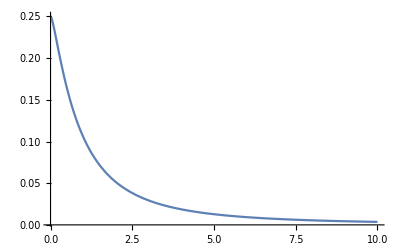

```mathematica
Plot[MeijerG[{{0},{}},{{0,1,3/2},{}},c^2]/(2 √π),{c,0,10},PlotRange-> All]
```

```mathematica
?MeijerG
```

```mathematica
Series[ζ ,{ϵ$s,0,1} ] // Normal // Expand // PowerExpand
```

-1-(2 ⅈ d^2 ϵ$s)/(λ$d^2 ψ^2)-(2 d^2 ϵ$s)/(λ$D^2 ψ^2)+(2 d √ϵ$s)/(λ$D ψ)

```mathematica
Series[ζ /. {ϵ$s-> 1/β} ,{β,0,2} ] // Normal // Expand // PowerExpand // Simplify
```

1-2 β+β^2 (2-(2 ⅈ λ$d^2)/λ$D^2+(2 ⅈ λ$d^3 ψ)/(λ$D^2 √(ⅈ d^2+λ$d^2 ψ^2)))

```mathematica
Series[ζ /. {ϵ$s-> 1/β^2} ,{β,0,4} ] // Normal // Expand // PowerExpand // Simplify
```

1-2 β^2+β^4 (2-(2 ⅈ λ$d^2)/λ$D^2+(2 ⅈ λ$d^3 ψ)/(λ$D^2 √(ⅈ d^2+λ$d^2 ψ^2)))

```mathematica
Series[ζ /. {ϵ$s-> β^2} ,{β,0,2} ] // Normal // Expand // PowerExpand // Simplify
```

-1-(2 d^2 β^2 (λ$d^2+ⅈ λ$D^2))/(λ$d^2 λ$D^2 ψ^2)+(2 d β)/(λ$D ψ)

```mathematica
Series[ζ ,{λ$D,0,2} ] // Normal // Expand // PowerExpand
```

1-(2 ⅈ λ$D^2)/λ$d^2-(2 λ$D ψ)/(d √ϵ$s)+(2 λ$D^2 ψ^2)/(d^2 ϵ$s)

```mathematica
Series[ζ ,{λ$D,λ$D$pk,1} ] // Normal // Expand // PowerExpand // Simplify
```

(d^2 √ϵ$s (-ⅈ λ$d^2+ϵ$s λ$D$pk^2) (-2 ⅈ λ$d^5 (λ$D-λ$D$pk) ψ+2 λ$d^3 λ$D$pk^2 (-2 ϵ$s λ$D+λ$D$pk+2 ϵ$s λ$D$pk) ψ+ⅈ √ϵ$s λ$d^4 √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2)-ⅈ √ϵ$s (-1+ϵ$s^2) λ$D$pk^4 √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2)-2 √ϵ$s λ$d^2 λ$D$pk (-2 λ$D+(2+ϵ$s) λ$D$pk) √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2))+λ$d^2 λ$D$pk^2 ψ^2 (4 ⅈ ϵ$s^(5/2) λ$d^3 (λ$D-λ$D$pk) λ$D$pk^2 ψ-2 ⅈ ϵ$s^(3/2) λ$d^3 λ$D$pk^3 ψ-λ$d^4 √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2)+2 ⅈ ϵ$s^3 λ$d^2 λ$D$pk^2 √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2)-ϵ$s^4 λ$D$pk^4 √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2)+ϵ$s^2 (λ$d^4-4 ⅈ λ$d^2 (λ$D-λ$D$pk) λ$D$pk+λ$D$pk^4) √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2)))/(√(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2) (λ$d^3 λ$D$pk ψ+√ϵ$s λ$d^2 √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2)+ⅈ √ϵ$s (1+ϵ$s) λ$D$pk^2 √(d^2 (λ$d^2+ⅈ ϵ$s λ$D$pk^2)+ϵ$s λ$d^2 λ$D$pk^2 ψ^2))^2)